## Ejercicio 1 : 1 Set de datos / Histograma

Antes de comenzar a correr cosas en este notebook, comentar que de principio a fin, en Mathematica Online, se necesitaron 6 minutos y medio en completar la evaluación completa.

```mathematica
beginning=Now;
SetDirectory[NotebookDirectory[]];
```

#### Datos de cuásares, ajuste a magnitudes en varias bandas.

```mathematica
rawdata=Import["astrostatistics.psu.edu_MSMA_datasets_SDSS_QSO.dat"];
```

```mathematica
header=rawdata[[1]]
```

{SDSS,z,u_mag,sig_u_mag,g_mag,sig_g_mag,r_mag,sig_r_mag,i_mag,sig_i_mag,z_mag,sig_z_mag,FIRST,ROSAT,Mp}

Buscar datos de magnitudes en r_, g_ y u_.

```mathematica
Position[header,"r_mag"]
Position[header,"g_mag"]
Position[header,"u_mag"]
```

{{7}}

{{5}}

{{3}}

Seleccionar datos en los que todas las bandas tengan valores mayores a 15:

```mathematica
data=Select[rawdata,NumberQ[#[[3]]]&&NumberQ[#[[5]]]&&NumberQ[#[[7]]]&&#[[3]]>15&&#[[5]]>15&&#[[7]]>15&]
```

Primero, trabajar con datos de banda u, encontrar una distribución con FindDistribution:

```mathematica
ufilter=data[[All,3]];
udist=SmoothKernelDistribution[ufilter];
bestdistu=FindDistribution[ufilter]
```

MixtureDistribution[{0.920482,0.0795176},{LogisticDistribution[19.5795,0.450639],LogNormalDistribution[3.14774,0.0537833]}]

Ajustar una distribución bimodal, comparar numéricamente y gráficamente.

```mathematica
umodel=MixtureDistribution[{a,b},{NormalDistribution[u1,s1],NormalDistribution[u2,s2]}];
```

```mathematica
Parallelize[mincuad=Sum[(PDF[udist,ufilter[[k]]]-PDF[umodel,ufilter[[k]]])^2,{k,Length@ufilter}]];
```

Parallelize::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
solOLSu=AbsoluteTiming[
NMinimize[mincuad,{{a,0.,1.},{b,0.,1.},{u1,18.,20.},{s1,0.,2.},{u2,19.,26.},{s2,0.,1.8}},Method->"SimulatedAnnealing"]]
```

{36.7161,{23.7274,{a→0.160499,b→1.08508,u1→19.3432,s1→0.257516,u2→19.6519,s2→0.991188}}}

```mathematica
mincuadbest=Sum[(PDF[udist,ufilter[[k]]]-PDF[bestdistu,ufilter[[k]]])^2,{k,Length@ufilter}]//Parallelize
```

Parallelize::nopar: No parallel kernels available; proceeding with sequential evaluation.

179.964

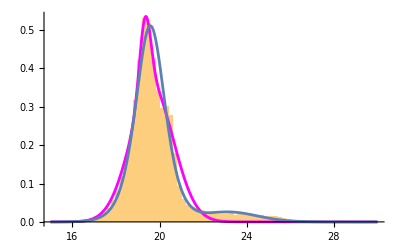

```mathematica
Show[
Histogram[ufilter,{15,30,0.2},"PDF",PlotRange->All],
Plot[PDF[umodel/.solOLSu[[2,2]],x],{x,15,30},PlotStyle->Magenta,PlotRange->All],
Plot[PDF[bestdistu,x],{x,15,30},PlotRange->All]
]
```

Ajustar una distribución tri-modal, comparar con las dos anteriores.

```mathematica
umodel2=MixtureDistribution[{a,b,c},{NormalDistribution[u1,s1],NormalDistribution[u2,s2],NormalDistribution[u3,s3]}];
```

```mathematica
Parallelize[mincuad2=Sum[(PDF[udist,ufilter[[k]]]-PDF[umodel2,ufilter[[k]]])^2,{k,Length@ufilter}]];
```

Parallelize::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
solOLSu2=AbsoluteTiming[
NMinimize[mincuad2,{{a,0.,1.},{b,0.,1.},{c,0,1},{u1,18.,20.},{s1,0.,2.},{u2,19.,26.},{s2,0.,1.8},{u3,19.,26.},{s3,0.,4}},Method->"SimulatedAnnealing"]]
```

{71.3675,{18.8176,{a→0.217805,b→1.52786,c→0.0862539,u1→19.3344,s1→0.25014,u2→19.6398,s2→0.922494,u3→23.7197,s3→0.888782}}}

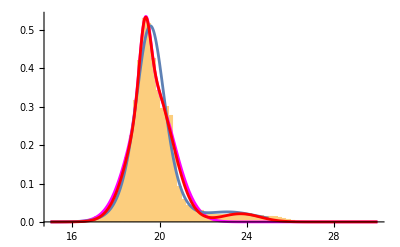

```mathematica
Show[
Histogram[ufilter,{15,30,0.2},"PDF"],
Plot[PDF[umodel/.solOLSu[[2,2]],x],{x,15,30},PlotStyle->Magenta,PlotRange->All],
Plot[PDF[bestdistu,x],{x,15,25},PlotRange->All],
Plot[PDF[umodel2/.solOLSu2[[2,2]],x],{x,15,30},PlotStyle->Red,PlotRange->All]
]
```

```mathematica
Show[Plot[PDF[umodel/.solOLSu[[2,2]],x],{x,15,30},PlotStyle->Magenta,PlotRange->All],
Plot[PDF[umodel2/.solOLSu2[[2,2]],x],{x,15,30},PlotStyle->Red,PlotRange->All]
]
```

-Graphics-

Como ejercicio propuesto: Realizar los mismos procedimientos para las bandas r_ y g_, iniciar con distribuciones bi-modales y, si su computador lo permite sin llegar a 90 °C, intentar  una trimodal. Intentar usar Maximum Likelihood como visto en clases (puede usar la función LogLikelihood[] para obtener la función a maximizar, sea consciente de las limitaciones de su ordenador, intente usar Paralellize cuando sea posible).

## Ejercicio 2: 2 set de datos / correlación.

Ahora, se intenta ajustar una función a dos variables (esperablemente) dependientes. En este caso, comprobar la Tercera Ley de Kepler (T.b2 ∝ D.b3):

```mathematica
exopl=Import["exoplanetas-11-2024.csv"];
```

```mathematica
header2=exopl[[1]]
```

{name,planet_status,mass,mass_error_min,mass_error_max,mass_sini,mass_sini_error_min,mass_sini_error_max,radius,radius_error_min,radius_error_max,orbital_period,orbital_period_error_min,orbital_period_error_max,semi_major_axis,semi_major_axis_error_min,semi_major_axis_error_max,eccentricity,eccentricity_error_min,eccentricity_error_max,inclination,inclination_error_min,inclination_error_max,angular_distance,discovered,updated,omega,omega_error_min,omega_error_max,tperi,tperi_error_min,tperi_error_max,tconj,tconj_error_min,tconj_error_max,tzero_tr,tzero_tr_error_min,tzero_tr_error_max,tzero_tr_sec,tzero_tr_sec_error_min,tzero_tr_sec_error_max,lambda_angle,lambda_angle_error_min,lambda_angle_error_max,impact_parameter,impact_parameter_error_min,impact_parameter_error_max,tzero_vr,tzero_vr_error_min,tzero_vr_error_max,k,k_error_min,k_error_max,temp_calculated,temp_calculated_error_min,temp_calculated_error_max,temp_measured,hot_point_lon,geometric_albedo,geometric_albedo_error_min,geometric_albedo_error_max,log_g,publication,detection_type,mass_measurement_type,radius_measurement_type,alternate_names,molecules,star_name,ra,dec,mag_v,mag_i,mag_j,mag_h,mag_k,star_distance,star_distance_error_min,star_distance_error_max,star_metallicity,star_metallicity_error_min,star_metallicity_error_max,star_mass,star_mass_error_min,star_mass_error_max,star_radius,star_radius_error_min,star_radius_error_max,star_sp_type,star_age,star_age_error_min,star_age_error_max,star_teff,star_teff_error_min,star_teff_error_max,star_detected_disc,star_magnetic_field,star_alternate_names}

```mathematica
Position[header2,"semi_major_axis"]
Position[header2,"orbital_period"]
```

{{15}}

{{12}}

```mathematica
orbdist=Select[exopl,NumberQ[#[[12]]]&&NumberQ[#[[15]]]&][[All,{12,15}]];
```

```mathematica
orbDvsT=ListPlot[orbdist]
```

-Graphics-

```mathematica
nlf=Fit[Log@orbdist,{x,1},x]
```

-3.97849+0.664651 x

```mathematica
nlf2=NonlinearModelFit[orbdist,a x^n,{n,a},x]
```

FittedModel[…]

```mathematica
Show[
ListLogLogPlot[orbdist],
Plot[nlf,{x,-10,15},PlotStyle->Red]]
```

-Graphics-

```mathematica
nlf2//Normal
```

0.0368935 x^0.60679

```mathematica
nlf1=E^nlf/.x->Log@x
```

0.0187139 x^0.664651

```mathematica
Show[
ListPlot[orbdist],
Plot[nlf2//Normal,{x,0,1000},PlotStyle->Red],
Plot[nlf1,{x,0,1000},PlotStyle->Blue]
]
```

-Graphics-

```mathematica
end=Now;
timeelapsed=end-beginning
```

6.55128 min